График итоговой функции

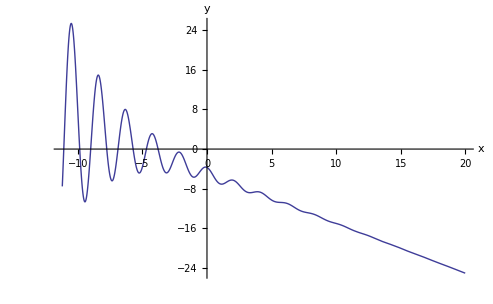

```mathematica
Clear[x,y,f];
f = -x-5+Cos[3*x]*8^(-(x-1)/8);
Plot[-x-5+Cos[3*x]*8^(-(x-1)/8),{x,-11.2,19.99}, AxesLabel->{x,y}]
```

Отображение графика и всех меток

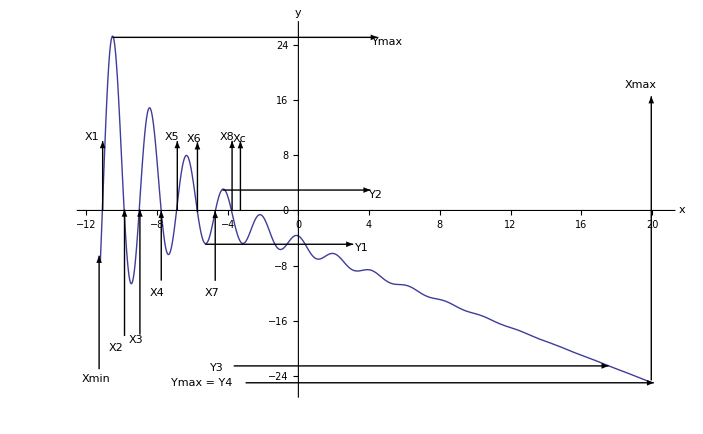

```mathematica
Graphics[{{{}, {}, {Hue[0.67, 0.6, 0.6], Line[{{-11.199999363469386, -7.518114366571952}, {-11.190433468057744, -6.930087632536919}, 
       {-11.1808675726461, -6.334166465806195}, {-11.161735781822816, -5.120805344198777}, {-11.123472200176245, -2.623324131004834}, 
       {-11.046945036883105, 2.5309269767518052}, {-11.037379141471463, 3.179371080169576}, {-11.027813246059821, 3.8269164212631837}, 
       {-11.008681455236536, 5.117157155025162}, {-10.970417873589966, 7.663403273278692}, {-10.893890710296827, 12.504966570131451}, 
       {-10.884324814885185, 13.077214119087092}, {-10.874758919473543, 13.640622533703294}, {-10.855627128650257, 14.739210329175213}, 
       {-10.817363547003687, 16.81205402251023}, {-10.807797651592043, 17.30210800109375}, {-10.798231756180401, 17.78017061956355}, 
       {-10.779099965357116, 18.698957338959495}, {-10.740836383710546, 20.37830471485621}, {-10.731270488298904, 20.763475115886173}, 
       {-10.72170459288726, 21.13424639888942}, {-10.702572802063976, 21.831631545786287}, {-10.693006906652332, 22.157798815396664}, 
       {-10.68344101124069, 22.468674015203106}, {-10.664309220417405, 23.04380457053828}, {-10.654743325005763, 23.307722565850696}, 
       {-10.64517742959412, 23.55567391331484}, {-10.635611534182477, 23.787524689718552}, {-10.626045638770835, 24.003154961386386}, 
       {-10.616479743359193, 24.202458814043425}, {-10.606913847947549, 24.385344370927623}, {-10.597347952535907, 24.5517337991949}, 
       {-10.587782057124265, 24.70156330466947}, {-10.577411530333332, 24.845230292375398}, {-10.5670410035424, 24.96933123136037}, 
       {-10.556670476751467, 25.073840550127326}, {-10.546299949960533, 25.158751867397065}, {-10.535929423169598, 25.224077895133526}, 
       {-10.525558896378666, 25.26985032352258}, {-10.515188369587733, 25.296119688112885}, {-10.5048178427968, 25.302955219344152}, 
       {-10.494447316005868, 25.290444674703796}, {-10.484076789214935, 25.25869415376862}, {-10.473706262424002, 25.207827896403344}, 
       {-10.463335735633068, 25.137988064402883}, {-10.452965208842134, 25.049334506879756}, {-10.442594682051201, 24.94204450971204}, 
       {-10.432224155260268, 24.81631252938137}, {-10.421853628469336, 24.672349911543744}, {-10.411483101678403, 24.510384594688833}, 
       {-10.40111257488747, 24.330660799256258}, {-10.390742048096538, 24.133438702589228}, {-10.380371521305603, 23.918994100117906}, 
       {-10.370000994514669, 23.68761805317618}, {-10.359630467723736, 23.43961652386569}, {-10.338889414141871, 22.895033092310108}, 
       {-10.328518887350938, 22.599134159115046}, {-10.318148360560004, 22.287974867644266}, {-10.297407306978137, 21.621385935647574}, 
       {-10.255925199814405, 20.122374564048027}, {-10.24555467302347, 19.71554695830627}, {-10.235184146232537, 19.296779014832833}, 
       {-10.214443092650672, 18.42527625233003}, {-10.172960985486938, 16.559840058994276}, {-10.089996771159473, 12.452221789983593}, 
       {-9.924068342504544, 3.677633422911394}, {-9.914385052956769, 3.1772845320900647}, {-9.904701763408994, 2.6808725446183623}, 
       {-9.885335184313444, 1.7014256098847502}, {-9.846602026122346, -0.19332854380093512}, {-9.836918736574571, -0.6515151504780565}, 
       {-9.827235447026798, -1.1027953071684236}, {-9.807868867931248, -1.9832848838225727}, {-9.769135709740148, -3.6469743884468766}, 
       {-9.759452420192373, -4.040850893841435}, {-9.749769130644598, -4.425335293816987}, {-9.730402551549048, -5.165054598087027}, 
       {-9.720719262001273, -5.519776970027827}, {-9.711035972453498, -5.864082509673127}, {-9.691669393357948, -6.520527425436988}, 
       {-9.681986103810173, -6.832234585625708}, {-9.672302814262398, -7.1326607451495345}, {-9.652936235166848, -7.69892108630385}, 
       {-9.643252945619073, -7.964407581694088}, {-9.633569656071298, -8.217917891026016}, {-9.61420307697575, -8.688434418971642}, 
       {-9.604519787427975, -8.905180473186276}, {-9.594836497880202, -9.109430122234505}, {-9.585153208332427, -9.30108111563576}, 
       {-9.575469918784652, -9.48004240042317}, {-9.565786629236877, -9.646234142133599}, {-9.556103339689102, -9.799587736178289}, 
       {-9.546420050141327, -9.940045809633112}, {-9.536736760593552, -10.067562213495142}, {-9.527053471045777, -10.182102005459797}, 
       {-9.517370181498002, -10.283641423280741}, {-9.507686891950227, -10.372167848782507}, {-9.498003602402452, -10.447679762603348}, 
       {-9.488320312854677, -10.510186689753137}, {-9.478637023306902, -10.559709136078611}, {-9.468953733759127, -10.59627851573552}, 
       {-9.459270444211352, -10.619937069774409}, {-9.449587154663577, -10.630737775953598}, {-9.439903865115802, -10.628744249899926}, 
       {-9.430220575568027, -10.614030637744525}, {-9.420537286020252, -10.586681500367508}, {-9.410853996472477, -10.546791689391823}, 
       {-9.401170706924702, -10.494466215072888}, {-9.39148741737693, -10.429820106236756}, {-9.381804127829154, -10.352978262425408}, 
       {-9.37212083828138, -10.264075298413918}, {-9.362437548733606, -10.163255381269364}, {-9.352754259185831, -10.050672060127278}, 
       {-9.343070969638056, -9.926488088866629}, {-9.333387680090281, -9.79087524186917}, {-9.323704390542506, -9.644014123054294}, 
       {-9.304337811446956, -9.317312442045061}, {-9.294844469601523, -9.141496382686599}, {-9.28535112775609, -8.955640217405909}, 
       {-9.266364444065225, -8.55464921038118}, {-9.256871102219792, -8.339952445766293}, {-9.24737776037436, -8.116091304639976}, 
       {-9.228391076683494, -7.641823338561922}, {-9.21889773483806, -7.391905309028129}, {-9.209404392992628, -7.133800036246914}, 
       {-9.190417709301762, -6.59406668964702}, {-9.152444341920031, -5.428058431702359}, {-9.142951000074598, -5.1201523186146485}, 
       {-9.133457658229165, -4.806258126411764}, {-9.1144709745383, -4.161681036897667}, {-9.076497607156568, -2.8137654879437264}, 
       {-9.000550872393106, 0.04818982366820057}, {-8.991057530547673, 0.41541503175457306}, {-8.98156418870224, 0.7837002553565884}, 
       {-8.962577505011375, 1.522199050057707}, {-8.924604137629643, 2.9982143109430845}, {-8.84865740286618, 5.878396324646465}, 
       {-8.839164061020748, 6.22596900831348}, {-8.829670719175315, 6.569838275004219}, {-8.81068403548445, 7.245391903943948}, 
       {-8.772710668102718, 8.540503431556933}, {-8.763217326257285, 8.851163272307918}, {-8.753723984411852, 9.156099632990227}, 
       {-8.734737300720987, 9.747895389467281}, {-8.696763933339257, 10.853176269411435}, {-8.686465960114534, 11.133606925786244}, 
       {-8.67616798688981, 11.405343864126225}, {-8.655572040440363, 11.921850171777557}, {-8.64527406721564, 12.166200856855113}, 
       {-8.634976093990916, 12.401020752017306}, {-8.61438014754147, 12.841341793305947}, {-8.604082174316746, 13.046505610304292}, 
       {-8.593784201092022, 13.241464192034886}, {-8.583486227867299, 13.426075194927577}, {-8.573188254642576, 13.600206958255937}, 
       {-8.562890281417852, 13.763738573355852}, {-8.552592308193129, 13.916559942163785}, {-8.531996361743682, 14.189685878137473}, 
       {-8.521698388518958, 14.309824679588854}, {-8.511400415294235, 14.418921745791135}, {-8.501102442069511, 14.516921536581142}, 
       {-8.490804468844788, 14.603779450102177}, {-8.480506495620064, 14.679461807173245}, {-8.47020852239534, 14.743945825267426}, 
       {-8.459910549170617, 14.797219582179778}, {-8.449612575945894, 14.839281969474717}, {-8.43931460272117, 14.870142635812018}, 
       {-8.429016629496447, 14.889821920259893}, {-8.418718656271723, 14.8983507757125}, {-8.408420683047, 14.89577068253819}, 
       {-8.398122709822276, 14.88213355259346}, {-8.387824736597553, 14.857501623746067}, {-8.37752676337283, 14.82194734505916}, 
       {-8.367228790148106, 14.775553252796373}, {-8.356930816923382, 14.71841183741581}, {-8.346632843698659, 14.650625401728554}, 
       {-8.336334870473936, 14.572305910404925}, {-8.326036897249212, 14.483574831018982}, {-8.315738924024489, 14.384562966828883}, 
       {-8.305440950799765, 14.275410281497571}, {-8.295142977575042, 14.156265715964933}, {-8.284845004350318, 14.02728699768891}, 
       {-8.274547031125595, 13.888640442479266}, {-8.264249057900871, 13.740500749153561}, {-8.243653111451424, 13.416481378042029}, 
       {-8.2333551382267, 13.24099106908766}, {-8.223057165001977, 13.05678590258557}, {-8.20246121855253, 12.663091207629813}, 
       {-8.192163245327807, 12.454049070172454}, {-8.181865272103083, 12.23718635456532}, {-8.161269325653636, 11.780964544120309}, 
       {-8.120077432754742, 10.785613173802686}, {-8.109779459530019, 10.521038399620693}, {-8.099481486305296, 10.250714211670692}, 
       {-8.078885539855849, 9.693941544990007}, {-8.037693646956955, 8.523960272372777}, {-8.028082910975389, 8.241720895504553}, 
       {-8.018472174993825, 7.956484820328501}, {-7.999250703030694, 7.378004409515356}, {-7.9608077591044335, 6.195931866899456}, 
       {-7.883921871251912, 3.7868745325571043}, {-7.874311135270347, 3.486332247666365}, {-7.8647003992887825, 3.1867286255956713}, 
       {-7.845478927325652, 2.591285519204254}, {-7.807035983399391, 1.4219612431341095}, {-7.73015009554687, -0.7808487306726408}, 
       {-7.720539359565305, -1.0394008319734036}, {-7.71092862358374, -1.2935712487599105}, {-7.6917071516206095, -1.7880418898377926}, 
       {-7.653264207694349, -2.7166977389381426}, {-7.643653471712784, -2.9353602625490396}, {-7.634042735731219, -3.1483202671972297}, 
       {-7.614821263768088, -3.5565724834384804}, {-7.576378319841828, -4.298801613411418}, {-7.566767583860263, -4.468201799952285}, 
       {-7.557156847878698, -4.6309286898139455}, {-7.537935375915567, -4.9359900914431245}, {-7.528324639934002, -5.078153716628504}, 
       {-7.518713903952436, -5.213302353453469}, {-7.499492431989307, -5.462281281458478}, {-7.489881696007742, -5.575990571987515}, 
       {-7.480270960026177, -5.682442911359914}, {-7.470660224044612, -5.781593566146678}, {-7.461049488063047, -5.873404125612627}, 
       {-7.451438752081482, -5.957842502293473}, {-7.441828016099917, -6.034882927287553}, {-7.432217280118351, -6.1045059402925865}, 
       {-7.422606544136786, -6.166698374421919}, {-7.412191176775931, -6.225700066368857}, {-7.401775809415074, -6.275966406451454}, 
       {-7.391360442054219, -6.317505474536094}, {-7.380945074693363, -6.350333867523474}, {-7.370529707332508, -6.374476637077302}, 
       {-7.360114339971652, -6.389967219395997}, {-7.349698972610796, -6.396847357139124}, {-7.339283605249941, -6.395167013627507}, 
       {-7.328868237889085, -6.384984279442922}, {-7.31845287052823, -6.366365271560081}, {-7.308037503167373, -6.339384025150098}, 
       {-7.297622135806518, -6.3041223782011615}, {-7.287206768445662, -6.260669849108405}, {-7.276791401084806, -6.209123507390988}, 
       {-7.26637603372395, -6.149587837700335}, {-7.2559606663630944, -6.082174597289104}, {-7.245545299002239, -6.007002667116098}, 
       {-7.235129931641383, -5.924197896767458}, {-7.224714564280527, -5.833892943379638}, {-7.214299196919671, -5.7362271047546844}, 
       {-7.203883829558816, -5.631346146862685}, {-7.193468462197959, -5.519402125931024}, {-7.172637727476248, -5.274963467422055}, 
       {-7.1622223601153925, -5.142802720707296}, {-7.151806992754537, -5.0042463022786965}, {-7.130976258032825, -4.708674226556395}, 
       {-7.089314788589402, -4.049062462865341}, {-7.078899421228546, -3.8710668031026856}, {-7.0684840538676905, -3.6882521660136627}, 
       {-7.0476533191459785, -3.3090315640987082}, {-7.005991849702555, -2.5024588765102758}, {-6.922668910815709, -0.7486410614286303}, 
       {-6.756023033042017, 2.895014139221269}, {-6.745797613383504, 3.1082556385286493}, {-6.735572193724989, 3.3190241725118117}, 
       {-6.715121354407962, 3.7323625443222737}, {-6.674219675773907, 4.520994354593545}, {-6.663994256115393, 4.709179206529409}, 
       {-6.653768836456879, 4.893432905412645}, {-6.6333179971398515, 5.24949942092811}, {-6.592416318505797, 5.907608975990724}, 
       {-6.5821908988472835, 6.0600531034140115}, {-6.571965479188769, 6.207400957421947}, {-6.551514639871742, 6.486325554507922}, 
       {-6.541289220213228, 6.617675184000726}, {-6.531063800554715, 6.743474468046164}, {-6.510612961237687, 6.9780311228108856}, 
       {-6.5003875415791725, 7.086607780978439}, {-6.490162121920659, 7.189272776941751}, {-6.479936702262146, 7.285950713794812}, 
       {-6.469711282603631, 7.376572255169196}, {-6.459485862945118, 7.461074158660924}, {-6.4492604432866045, 7.539399303318469}, 
       {-6.43903502362809, 7.611496711196902}, {-6.428809603969577, 7.67732156298959}, {-6.418584184311063, 7.736835207754067}, 
       {-6.408358764652549, 7.790005166753957}, {-6.398133344994036, 7.836805131444834}, {-6.387907925335522, 7.87721495563662}, 
       {-6.377682505677008, 7.911220641871156}, {-6.3674570860184945, 7.938814322058195}, {-6.357231666359981, 7.959994232418778}, 
       {-6.347006246701467, 7.9747646827897425}, {-6.336780827042952, 7.983136020348313}, {-6.326555407384439, 7.985124587820733}, 
       {-6.316329987725926, 7.980752676243526}, {-6.306104568067411, 7.970048472351115}, {-6.295879148408898, 7.953046000667916}, 
       {-6.285653728750384, 7.929785060387773}, {-6.27542830909187, 7.9003111571280416}, {-6.265202889433357, 7.864675429650057}, 
       {-6.254977469774843, 7.822934571641886}, {-6.244752050116329, 7.775150748663566}, {-6.2345266304578155, 7.721391510358996}, 
       {-6.224301210799302, 7.661729698042511}, {-6.214075791140788, 7.5962433477721545}, {-6.203850371482274, 7.525015589025108}, 
       {-6.183399532165247, 7.365693193329945}, {-6.173174112506732, 7.277789311348032}, {-6.162948692848219, 7.18452529934111}, 
       {-6.142497853531191, 6.982349010503257}, {-6.132272433872678, 6.873663667756487}, {-6.122047014214164, 6.760071802611942}, 
       {-6.101596174897137, 6.518667357417375}, {-6.092057992481781, 6.399825539525237}, {-6.082519810066426, 6.27715691799986}, 
       {-6.063443445235714, 6.02078983325733}, {-6.025290715574293, 5.467224418106904}, {-5.94898525625145, 4.224789787762051}, 
       {-5.939447073836094, 4.059363011565276}, {-5.929908891420739, 3.8921401057607716}, {-5.910832526590028, 3.552861117474429}, 
       {-5.872679796928606, 2.8588882920229723}, {-5.796374337605763, 1.440781504703641}, {-5.786836155190407, 1.2634189983835424}, 
       {-5.777297972775052, 1.0864944414040343}, {-5.758221607944341, 0.7345002974164324}, {-5.72006887828292, 0.041649931685500574}, 
       {-5.710530695867565, -0.12848436496642002}, {-5.700992513452209, -0.2971339374145039}, {-5.681916148621498, -0.6294865263406915}, 
       {-5.643763418960076, -1.2710721459530814}, {-5.6342252365447205, -1.4259829791100853}, {-5.624687054129366, -1.5784795397865952}, 
       {-5.605610689298654, -1.8758096785354708}, {-5.567457959637233, -2.437026221738574}, {-5.557919777221878, -2.5698138325952216}, 
       {-5.548381594806522, -2.699418194702315}, {-5.529305229975812, -2.948748070355673}, {-5.4911525003143895, -3.4057649694704497}, 
       {-5.480809686519743, -3.519639289733502}, {-5.470466872725098, -3.629088757550752}, {-5.449781245135805, -3.8344293161979186}, 
       {-5.439438431341159, -3.9301903790637605}, {-5.429095617546513, -4.021266608318242}, {-5.408409989957221, -4.189157543490813}, 
       {-5.398067176162575, -4.265880926061403}, {-5.387724362367929, -4.33773686435671}, {-5.3773815485732825, -4.404691957222272}, 
       {-5.367038734778637, -4.46671772325268}, {-5.3566959209839915, -4.523790601960328}, {-5.346353107189345, -4.575891950177861}, 
       {-5.336010293394699, -4.623008033723284}, {-5.325667479600053, -4.6651300143612895}, {-5.315324665805408, -4.702253932098635}, 
       {-5.304981852010761, -4.734380682855619}, {-5.294639038216115, -4.761515991560142}, {-5.284296224421469, -4.783670380714918}, 
       {-5.273953410626823, -4.800859134492484}, {-5.2636105968321765, -4.813102258416709}, {-5.253267783037531, -4.820424434693532}, 
       {-5.2429249692428845, -4.822854973257409}, {-5.232582155448238, -4.8204277586038184}, {-5.222239341653593, -4.813181192481857}, 
       {-5.211896527858946, -4.8011581325245505}, {-5.2015537140643, -4.7844058268980305}, {-5.191210900269654, -4.762975845054137}, 
       {-5.180868086475008, -4.736924004674328}, {-5.170525272680361, -4.706310294895994}, {-5.160182458885716, -4.671198795915362}, 
       {-5.14983964509107, -4.631657595064193}, {-5.139496831296424, -4.587758699460378}, {-5.129154017501778, -4.539577945335271}, 
       {-5.118811203707132, -4.487194904143328}, {-5.108468389912486, -4.430692785562052}, {-5.098125576117839, -4.370158337492859}, 
       {-5.077439948528547, -4.237356515531653}, {-5.067097134733901, -4.1652793888530075}, {-5.056754320939255, -4.089550207955793}, 
       {-5.0360686933499625, -3.927549933534466}, {-4.994697438171379, -3.56443621166127}, {-4.984354624376733, -3.466175254005631}, 
       {-4.974011810582087, -3.365158938480819}, {-4.953326182992795, -3.155352100374353}, {-4.91195492781421, -2.7081831658058313}, 
       {-4.829212417457041, -1.7330780250713909}, {-4.819556840905554, -1.614697026577171}, {-4.809901264354066, -1.4957477513825368}, 
       {-4.79059011125109, -1.2565893351849768}, {-4.7519678050451395, -0.7763329867164045}, {-4.6747231926332375, 0.1676040142249488}, 
       {-4.66506761608175, 0.28198495925376477}, {-4.655412039530262, 0.3952246762434376}, {-4.636100886427286, 0.6178903198398137}, 
       {-4.597478580221336, 1.0453257370027704}, {-4.587823003669849, 1.1479263845057626}, {-4.578167427118361, 1.2486494998963313}, 
       {-4.558856274015385, 1.4441305278712748}, {-4.520233967809434, 1.809022806112865}, {-4.510578391257946, 1.8943804807213525}, 
       {-4.500922814706458, 1.9772524214842684}, {-4.481611661603482, 2.135279290898612}, {-4.471956085051994, 2.2103105539554337}, 
       {-4.4623005085005065, 2.282608831216985}, {-4.442989355397532, 2.4187873813473777}, {-4.433333778846045, 2.4825647336736507}, 
       {-4.423678202294557, 2.54340331942132}, {-4.414022625743069, 2.601258412746845}, {-4.404367049191581, 2.6560880274073546}, 
       {-4.394711472640093, 2.707852938446031}, {-4.3850558960886055, 2.75651670144062}, {-4.36574474298563, 2.844409006684153}, 
       {-4.356089166434142, 2.8835787018157526}, {-4.346433589882654, 2.919529576072057}, {-4.336778013331166, 2.952239290974831}, 
       {-4.327122436779679, 2.9816883528164344}, {-4.317466860228192, 3.007860114853106}, {-4.307811283676704, 3.0307407770866757}, 
       {-4.2981557071252166, 3.0503193836470515}, {-4.288500130573729, 3.066587817789659}, {-4.278844554022241, 3.0795407945239828}, 
       {-4.269188977470753, 3.089175850891319}, {-4.259533400919265, 3.0954933339116772}, {-4.249877824367777, 3.0984963862216848}, 
       {-4.240222247816289, 3.098190929427156}, {-4.230566671264802, 3.0945856451958065}, {-4.220911094713314, 3.0876919541173735}, 
       {-4.211255518161827, 3.077523992360146}, {-4.20178988931268, 3.0643939858849953}, {-4.1923242604635345, 3.048151765625297}, 
       {-4.182858631614389, 3.028818100217671}, {-4.173393002765243, 3.006416161615941}, {-4.163927373916097, 2.9809714945156935}, 
       {-4.154461745066952, 2.9525119840060934}, {-4.144996116217806, 2.9210678214838497}, {-4.13553048736866, 2.886671468865519}, 
       {-4.1260648585195145, 2.849357621135466}, {-4.116599229670369, 2.809163167268031}, {-4.097667971972077, 2.720290721438843}, 
       {-4.088202343122932, 2.6716971037143793}, {-4.078736714273786, 2.620391539440214}, {-4.059805456575495, 2.5098353736736807}, 
       {-4.050339827726349, 2.450684943295656}, {-4.040874198877203, 2.389022808736443}, {-4.021942941178912, 2.2583836644082877}, 
       {-3.984080425782329, 1.9694809645964226}, {-3.9746147969331833, 1.8918591421190145}, {-3.9651491680840376, 1.8122077845309876}, 
       {-3.946217910385746, 1.6470850863220088}, {-3.9083553949891634, 1.2955073546338727}, {-3.8988897661400177, 1.2035871338854265}, 
       {-3.889424137290872, 1.110203964470506}, {-3.8704928795925806, 0.9193502824821604}, {-3.832630364195998, 0.5234427163374586}, 
       {-3.756905333402832, -0.3075766064566461}, {-3.6054552718165005, -1.984642535703772}, {-3.5951850115880637, -2.0931422154285197}, 
       {-3.5849147513596273, -2.200462305267997}, {-3.5643742309027546, -2.411220239987648}, {-3.523293189989009, -2.814900111693543}, 
       {-3.513022929760573, -2.911645333859134}, {-3.5027526695321365, -3.0065712306576042}, {-3.4822121490752638, -3.1906830000849866}, 
       {-3.4411311081615183, -3.534097226197977}, {-3.430860847933082, -3.614424047976492}, {-3.4205905877046456, -3.692427022441826}, 
       {-3.400050067247773, -3.8412550551685394}, {-3.3897798070193366, -3.9119833212211526}, {-3.3795095467909, -3.9801942205862737}, 
       {-3.3589690263340275, -4.108899145282501}, {-3.348698766105591, -4.169317466581842}, {-3.338428505877155, -4.227067056843707}, 
       {-3.317887985420282, -4.334438483167043}, {-3.3076177251918457, -4.384006402527784}, {-3.2973474649634094, -4.430797779623146}, 
       {-3.2768069445065366, -4.515973483893209}, {-3.2665366842781003, -4.554326036625438}, {-3.256266424049664, -4.589838498960756}, 
       {-3.2459961638212276, -4.622501917858693}, {-3.235725903592791, -4.652310105387247}, {-3.225455643364355, -4.679259629901142}, 
       {-3.2151853831359185, -4.703349804638049}, {-3.204915122907482, -4.724582673757489}, {-3.194644862679046, -4.742962995849272}, 
       {-3.1843746024506094, -4.758498224940739}, {-3.174104342222173, -4.771198489034191}, {-3.1638340819937367, -4.781076566208169}, 
       {-3.1535638217653004, -4.788147858318316}, {-3.143293561536864, -4.792430362335727}, {-3.1330233013084277, -4.793944639362654}, 
       {-3.1227530410799913, -4.792713781367533}, {-3.112482780851555, -4.788763375683192}, {-3.1022125206231186, -4.782121467313983}, 
       {-3.0919422603946822, -4.772818519099518}, {-3.081672000166246, -4.760887369784344}, {-3.0714017399378095, -4.746363190044773}, 
       {-3.061131479709373, -4.7292834365256295}, {-3.050861219480937, -4.70968780394139}, {-3.0405909592525004, -4.687618175297681}, 
       {-3.030320699024064, -4.663118570290658}, {-3.0200504387956277, -4.636235091943128}, {-3.0097801785671914, -4.607015871537783}, 
       {-2.999509918338755, -4.575511011909041}, {-2.9892396581103187, -4.541772529156428}, {-2.9789693978818823, -4.505854292843383}, 
       {-2.968699137653446, -4.467811964746718}, {-2.948158617196573, -4.385586264257281}, {-2.9385755942112946, -4.344530677416865}, 
       {-2.9289925712260168, -4.301830422065252}, {-2.9098265252554603, -4.211703367823441}, {-2.871494433314348, -4.014052294880927}, 
       {-2.8619114103290704, -3.9613403997270655}, {-2.852328387343792, -3.9074237097645863}, {-2.833162341373236, -3.7962115218061747}, 
       {-2.794830249432124, -3.5619549590561643}, {-2.785247226446846, -3.5012823879390256}, {-2.775664203461568, -3.4398903756765176}, 
       {-2.756498157491012, -3.3151983667726226}, {-2.7181660655499, -3.059944958471728}, {-2.6415018816676756, -2.5400716024298315}, 
       {-2.631918858682398, -2.475426488633047}, {-2.6223358356971196, -2.4110610880411394}, {-2.6031697897265635, -2.2834089677589353}, 
       {-2.5648376977854515, -2.0340611492716487}, {-2.5552546748001737, -1.9732988739350663}, {-2.5456716518148954, -1.9132777521600346}, 
       {-2.5265056058443394, -1.7956745559589473}, {-2.4881735139032273, -1.5716792177712897}, {-2.4785904909179495, -1.5183070171689568}, 
       {-2.4690074679326712, -1.4660808312025488}, {-2.449841421962115, -1.3652478576174605}, {-2.4402583989768374, -1.3167286748843188}, 
       {-2.430675375991559, -1.2695306560397683}, {-2.411509330021003, -1.1792591613875456}, {-2.4019263070357253, -1.1362628532835382}, 
       {-2.392343284050447, -1.0947419937567662}, {-2.373177238079891, -1.0162656471600489}, {-2.3635942150946128, -0.9793760797069639}, 
       {-2.3540111921093345, -0.9440937596208769}, {-2.3348451461387785, -0.8784664662352062}, {-2.3244574917742096, -0.8457098854617602}, 
       {-2.314069837409641, -0.8149710362549274}, {-2.3036821830450727, -0.7862791792635109}, {-2.2932945286805038, -0.7596614202923635}, 
       {-2.282906874315935, -0.7351426954602209}, {-2.2725192199513664, -0.7127457585544432}, {-2.262131565586798, -0.6924911705831529}, 
       {-2.251743911222229, -0.6743972915231629}, {-2.24135625685766, -0.6584802742598947}, {-2.2309686024930917, -0.6447540607133959}, 
       {-2.2205809481285232, -0.6332303801424755}, {-2.2101932937639543, -0.6239187496168759}, {-2.1998056393993854, -0.6168264766453353}, 
       {-2.189417985034817, -0.6119586639453876}, {-2.1790303306702485, -0.6093182163386834}, {-2.1686426763056796, -0.6089058497536795}, 
       {-2.1582550219411107, -0.6107201023155571}, {-2.1478673675765423, -0.6147573475012984}, {-2.137479713211974, -0.621011809335982}, 
       {-2.127092058847405, -0.6294755796044527}, {-2.116704404482836, -0.6401386370507471}, {-2.1063167501182676, -0.6529888685358078}, 
       {-2.095929095753699, -0.6680120921223214}, {-2.0855414413891302, -0.6851920820537569}, {-2.0751537870245613, -0.704510595593046}, 
       {-2.064766132659993, -0.7259474016846936}, {-2.0543784782954244, -0.7494803114025443}, {-2.0439908239308555, -0.7750852101438626}, 
       {-2.0336031695662866, -0.8027360915289226}, {-2.023215515201718, -0.8324050929638469}, {-2.002440206472581, -0.8976769492061787}, 
       {-1.9920525521080121, -0.9332151402235551}, {-1.9816648977434435, -0.9706422057621054}, {-1.960889589014306, -1.0510151294044723}, 
       {-1.9505019346497374, -1.093883091808163}, {-1.9401142802851687, -1.138484230435005}, {-1.9193389715560314, -1.2327137514809572}, 
       {-1.9089513171914627, -1.2822524938284985}, {-1.898563662826894, -1.3333452347330288}, {-1.8777883540977567, -1.4399991606832256}, 
       {-1.836237736639482, -1.6697612297458764}, {-1.8258500822749133, -1.730321660451432}, {-1.8154624279103446, -1.792020630904032}, 
       {-1.7946871191812073, -1.9186086522583548}, {-1.7531365017229326, -2.1829274033802273}, {-1.6700352668063831, -2.742774347471697}, 
       {-1.6598375601441564, -2.813182222457324}, {-1.6496398534819299, -2.8837673150094854}, {-1.6292444401574766, -3.025238445343704}, 
       {-1.5884536135085698, -3.307783291805592}, {-1.5068719602107565, -3.8588186300623755}, {-1.4966742535485298, -3.925336979550475}, 
       {-1.486476546886303, -3.991160683997099}, {-1.4660811335618498, -4.120530563355075}, {-1.425290306912943, -4.368860782707349}, 
       {-1.4150926002507163, -4.428516381894144}, {-1.4048948935884897, -4.487117152940965}, {-1.3844994802640365, -4.60099568809753}, 
       {-1.3437086536151297, -4.814422184761725}, {-1.3335109469529032, -4.864592307457576}, {-1.3233132402906764, -4.913424390054285}, 
       {-1.302917826966223, -5.006958847746386}, {-1.2927201203039962, -5.0516070490135165}, {-1.2825224136417697, -5.09480889813901}, 
       {-1.2621270003173164, -5.176781487414226}, {-1.2519292936550896, -5.215509978427622}, {-1.241731586992863, -5.25270764276745}, 
       {-1.2213361736684096, -5.322442852206606}, {-1.211138467006183, -5.3549504525821465}, {-1.2009407603439564, -5.385867348599108}, 
       {-1.1805453470195029, -5.442886297911129}, {-1.1703476403572761, -5.468970899191326}, {-1.1601499336950496, -5.493429891943596}, 
       {-1.149952227032823, -5.516258460080579}, {-1.1397545203705963, -5.537453346224329}, {-1.1295568137083696, -5.557012846528091}, 
       {-1.1193591070461428, -5.574936804064512}, {-1.109161400383916, -5.591226600794109}, {-1.0989636937216896, -5.605885148129027}, 
       {-1.088765987059463, -5.618916876108401}, {-1.0785682803972363, -5.630327721202846}, {-1.0683705737350095, -5.640125112766779}, 
       {-1.0581728670727828, -5.6483179581584775}, {-1.047975160410556, -5.6549166265489}, {-1.0377774537483295, -5.659932931441432}, 
       {-1.027579747086103, -5.663380111925816}, {-1.0173820404238763, -5.665272812690577}, {-1.007871571004808, -5.665651190268296}, 
       {-0.9983611015857397, -5.66470554394688}, {-0.9888506321666712, -5.662450957557217}, {-0.9793401627476029, -5.658903511345626}, 
       {-0.9698296933285346, -5.654080263904821}, {-0.9603192239094662, -5.647999233393634}, {-0.9508087544903979, -5.640679378064351}, 
       {-0.9412982850713296, -5.632140576117036}, {-0.9317878156522612, -5.622403604900624}, {-0.9222773462331929, -5.6114901194810205}, 
       {-0.9127668768141246, -5.599422630596867}, {-0.9032564073950562, -5.586224482024026}, {-0.8937459379759879, -5.571919827370216}, 
       {-0.8842354685569196, -5.556533606321593}, {-0.8652145297187829, -5.522620007997241}, {-0.8557040602997146, -5.504146219477417}, 
       {-0.8461935908806462, -5.484697991089914}, {-0.8271726520425096, -5.442992832669747}, {-0.7891307743662361, -5.349183980930623}, 
       {-0.7796203049471678, -5.3237461249518265}, {-0.7701098355280995, -5.297577997618779}, {-0.7510888966899628, -5.243182494994494}, 
       {-0.7130470190136895, -5.127096719466036}, {-0.7035365495946212, -5.096755639446411}, {-0.6940260801755529, -5.065956406990615}, 
       {-0.6750051413374162, -5.003124600241052}, {-0.6369632636611429, -4.87352340205565}, {-0.5608795083085961, -4.606576887598238}, 
       {-0.5513690388895278, -4.573176157755986}, {-0.5418585694704594, -4.53988517529592}, {-0.5228376306323228, -4.473770058187215}, 
       {-0.4847957529560495, -4.344352851168074}, {-0.4752852835369812, -4.312777391973968}, {-0.4657748141179128, -4.2815779451094}, 
       {-0.44675387527977617, -4.220432396706206}, {-0.4087119976035028, -4.1040032185809405}, {-0.3983968968051438, -4.073970356101347}, 
       {-0.38808179600678483, -4.04466093407617}, {-0.3674515944100669, -3.988348520684195}, {-0.35713649361170796, -3.961411276237527}, 
       {-0.34682139281334895, -3.935328912730308}, {-0.326191191216631, -3.8858496040450854}, {-0.315876090418272, -3.8625104871149762}, 
       {-0.305560989619913, -3.8401418629563846}, {-0.28493078802319505, -3.7984200179183176}, {-0.2746156872248361, -3.77911599261622}, 
       {-0.2643005864264771, -3.760880815764968}, {-0.2436703848297591, -3.727702854276723}, {-0.23335528403140013, -3.712800065372574}, 
       {-0.22304018323304114, -3.6990460904439466}, {-0.2127250824346822, -3.686457943409966}, {-0.2024099816363232, -3.6750514255074362}, 
       {-0.19209488083796422, -3.664841116573321}, {-0.18177978003960527, -3.6558403675489997}, {-0.17146467924124628, -3.6480612942069923}, 
       {-0.1611495784428873, -3.641514772099632}, {-0.15083447764452831, -3.6362104327280225}, {-0.14051937684616933, -3.632156660928435}, 
       {-0.13020427604781035, -3.629360593472155}, {-0.11988917524945138, -3.627828118873626}, {-0.10957407445109241, -3.62756387840062}, 
       {-0.09925897365273342, -3.628571268279038}, {-0.08894387285437444, -3.630852443083816}, {-0.07862877205601546, -3.6344083203063446}, 
       {-0.06831367125765647, -3.6392385860877154}, {-0.057998570459297495, -3.645341702106025}, {-0.04768346966093852, -3.6527149136049646}, 
       {-0.037368368862579535, -3.6613542585498506}, {-0.027053268064220558, -3.6712545778962506}, {-0.016738167265861578, -3.682409526955398}, 
       {-0.006423066467502599, -3.6948115878395758}, {0.0038920343308563796, -3.708452082969716}, {0.014207135129215358, -3.723321189626563}, 
       {0.024522235927574337, -3.7394079555257873}, {0.03483733672593332, -3.7567003153966096}, {0.045152437524292294, -3.775185108542618}, 
       {0.05546753832265128, -3.794848097362606}, {0.06578263912101026, -3.8156739868085134}, {0.08641284071772821, -3.860748123268126}, 
       {0.09672794151608718, -3.88496068071209}, {0.10704304231444617, -3.910264804727862}, {0.12767324391116414, -3.9640657928019536}, 
       {0.16893364710460004, -4.083814794640459}, {0.17924874790295903, -4.116142781157767}, {0.18956384870131798, -4.149375899312216}, 
       {0.21019405029803595, -4.218449265102526}, {0.2514544534914719, -4.366229100669617}, {0.2610823170466725, -4.402403202165874}, 
       {0.2707101806018732, -4.439164655214799}, {0.2899659077122745, -4.514346552043822}, {0.3284773619330771, -4.670606993007931}, 
       {0.4055002703746822, -5.000596004817139}, {0.4151281339298829, -5.042937507496936}, {0.4247559974850835, -5.085427714714836}, 
       {0.44401172459548477, -5.170741110676016}, {0.48252317881628737, -5.341911471574436}, {0.5595460872578926, -5.6802348224398225}, 
       {0.5691739508130932, -5.721624848695668}, {0.5788018143682938, -5.762728488260609}, {0.5980575414786952, -5.843977159369946}, 
       {0.6365689956994978, -6.001966562749297}, {0.6461968592546984, -6.040389538413011}, {0.655824722809899, -6.078338272714714}, 
       {0.6750804499203003, -6.152728037307577}, {0.7135919041411029, -6.294911954048089}, {0.7232197676963035, -6.3289727401949305}, 
       {0.7328476312515042, -6.362403698867905}, {0.7521033583619054, -6.427309515030618}, {0.7906148125827079, -6.548866038601084}, 
       {0.8002426761379086, -6.577453248273517}, {0.8098705396931092, -6.605294213849502}, {0.8291262668035105, -6.658691931579738}, 
       {0.8676377210243131, -6.75607124832845}, {0.8780702159588044, -6.780233915067802}, {0.8885027108932957, -6.80343446888247}, 
       {0.9093677007622782, -6.8469207850924585}, {0.9198001956967695, -6.867194806830869}, {0.9302326906312608, -6.886483235128695}, 
       {0.9510976805002435, -6.922090764660799}, {0.9615301754347347, -6.938406068498469}, {0.9719626703692261, -6.95372817712917}, 
       {0.9823951653037174, -6.968057650474246}, {0.9928276602382087, -6.9813960223124125}, {1.0032601551727, -6.993745793502948}, 
       {1.0136926501071912, -7.0051104242938145}, {1.0241251450416824, -7.015494325727203}, {1.0345576399761738, -7.024902850155858}, 
       {1.0449901349106652, -7.033342280884326}, {1.0554226298451563, -7.040819820950048}, {1.0658551247796475, -7.0473435810599945}, 
       {1.0762876197141389, -7.052922566699273}, {1.0867201146486303, -7.057566664428891}, {1.0971526095831214, -7.061286627390526}, 
       {1.1075851045176126, -7.0640940600368705}, {1.118017599452104, -7.066001402106759}, {1.1284500943865954, -7.067021911864946}, 
       {1.1388825893210865, -7.06716964862698}, {1.1493150842555777, -7.066459454590273}, {1.159747579190069, -7.064906935992967}, 
       {1.1701800741245605, -7.062528443622804}, {1.1806125690590519, -7.059341052698661}, {1.1910450639935433, -7.055362542147992}, 
       {1.2014775589280344, -7.050611373303783}, {1.2119100538625256, -7.045106668045171}, {1.222342548797017, -7.038868186406215}, 
       {1.2327750437315084, -7.031916303677761}, {1.2432075386659998, -7.02427198702765}, {1.2536400336004911, -7.015956771664901}, 
       {1.2640725285349823, -7.006992736573787}, {1.2849375184039649, -6.987209093623453}, {1.2953700133384562, -6.976436138720155}, 
       {1.3058025082729474, -6.965107618880478}, {1.32666749814193, -6.940881957687541}, {1.368397477879895, -6.886863046176055}, 
       {1.3788299728143865, -6.872349357398477}, {1.3892624677488776, -6.857484907489138}, {1.4101274576178602, -6.826811069224918}, 
       {1.4518574373558253, -6.762443254159489}, {1.5353173968317557, -6.627753468402535}, {1.5455599440639052, -6.611196710612483}, 
       {1.5558024912960544, -6.594720003888053}, {1.5762875857603529, -6.5621062025468895}, {1.6172577746889498, -6.498919039555097}, 
       {1.627500321921099, -6.483686004860866}, {1.6377428691532483, -6.468724692070602}, {1.658227963617547, -6.439706702692561}, 
       {1.6991981525461441, -6.385892211706937}, {1.7094406997782934, -6.373438434708691}, {1.7196832470104426, -6.361423943707297}, 
       {1.7401683414747413, -6.33878741258677}, {1.7504108887068908, -6.328201318695077}, {1.76065343593904, -6.318126374905599}, 
       {1.7811385304033385, -6.299575589723282}, {1.7913810776354877, -6.291131090929727}, {1.801623624867637, -6.283260404018186}, 
       {1.8118661720997862, -6.275977665266652}, {1.8221087193319356, -6.269296378111423}, {1.832351266564085, -6.263229403697496}, 
       {1.8425938137962343, -6.257788952088463}, {1.8528363610283836, -6.252986574140753}, {1.8630789082605328, -6.248833154046402}, 
       {1.873321455492682, -6.2453389025478625}, {1.8835640027248313, -6.2425133508277355}, {1.8938065499569805, -6.240365345075633}, 
       {1.90404909718913, -6.2389030417337175}, {1.9142916444212794, -6.23813390342185}, {1.9245341916534286, -6.2380646955425725}, 
       {1.9347767388855779, -6.238701483565563}, {1.9450192861177271, -6.240049630990511}, {1.9552618333498764, -6.242113797986756}, 
       {1.9655043805820256, -6.244897940707376}, {1.9757469278141748, -6.248405311274804}, {1.9859894750463243, -6.252638458434412}, 
       {1.9962320222784737, -6.2575992288719045}, {2.006474569510623, -6.263288769189729}, {2.016717116742772, -6.269707528537154}, 
       {2.0269596639749214, -6.276855261888028}, {2.037202211207071, -6.284731033959678}, {2.0474447584392204, -6.293333223765817}, 
       {2.0576873056713696, -6.302659529795803}, {2.067929852903519, -6.312706975811958}, {2.078172400135668, -6.323471917256221}, 
       {2.0884149473678173, -6.334950048256781}, {2.1089000418321158, -6.360025395031413}, {2.119142589064265, -6.373610763752568}, 
       {2.1293851362964142, -6.387885645973061}, {2.1498702307607127, -6.418473395422146}, {2.19084041968931, -6.487553564109955}, 
       {2.200395729678301, -6.505127519647417}, {2.209951039667292, -6.523235890594078}, {2.229061659645274, -6.561016648905146}, 
       {2.2672828996012377, -6.642538633508403}, {2.343725379513165, -6.8267741413038125}, {2.3532806895021556, -6.851537401861919}, 
       {2.3628359994911468, -6.876639642212243}, {2.3819466194691286, -6.927802793282366}, {2.4201678594250926, -7.033545655062099}, 
       {2.4966103393370203, -7.255234822503188}, {2.506165649326011, -7.2835939772750065}, {2.515720959315002, -7.312043755397381}, 
       {2.534831579292984, -7.369150991664851}, {2.573052819248948, -7.4837485936565775}, {2.6494952991608756, -7.710956270826318}, 
       {2.6590506091498662, -7.7388726748334955}, {2.6686059191388574, -7.766632180977916}, {2.687716539116839, -7.821623689736209}, 
       {2.7259377790728028, -7.929111478080009}, {2.8023802589847304, -8.131237814417691}, {2.812740200353012, -8.157060838674184}, 
       {2.8231001417212935, -8.182466639511658}, {2.843820024457857, -8.231977609516948}, {2.8852597899309833, -8.32548184384547}, 
       {2.8956197312992646, -8.347648628782244}, {2.9059796726675464, -8.36931329667695}, {2.9266995554041095, -8.411103723599826}, 
       {2.9681393208772358, -8.488331508259334}, {2.978499262245517, -8.506280193644372}, {2.988859203613799, -8.52367590016174}, 
       {3.009579086350362, -8.556793505290905}, {3.0199390277186438, -8.572509371287072}, {3.0302989690869255, -8.587660193009992}, 
       {3.0510188518234886, -8.616260803793233}, {3.0613787931917704, -8.629709037511208}, {3.0717387345600518, -8.642589111790343}, 
       {3.0924586172966153, -8.666647753212615}, {3.1028185586648966, -8.677829170793434}, {3.1131785000331784, -8.688448121184019}, 
       {3.1338983827697415, -8.708010227823623}, {3.144258324138023, -8.716960502538736}, {3.1546182655063046, -8.725362534444246}, 
       {3.1649782068745864, -8.73322116846231}, {3.1753381482428678, -8.740541750866129}, {3.185698089611149, -8.747330121398424}, 
       {3.196058030979431, -8.753592604953367}, {3.2064179723477126, -8.759336002832313}, {3.216777913715994, -8.764567583584162}, 
       {3.2271378550842753, -8.76929507344143}, {3.237497796452557, -8.773526646363527}, {3.247857737820839, -8.77727091369897}, 
       {3.25821767918912, -8.780536913478645}, {3.268577620557402, -8.783334099352468}, {3.2789375619256838, -8.785672329182109}, 
       {3.289297503293965, -8.787561853302696}, {3.299657444662247, -8.789013302466667}, {3.3100173860305286, -8.790037675483193}, 
       {3.32037732739881, -8.790646326566748}, {3.3307372687670918, -8.790850952408764}, {3.3410972101353735, -8.790663578986303}, 
       {3.351457151503655, -8.79009654812203}, {3.3618170928719366, -8.789162503809836}, {3.3721770342402184, -8.787874378320664}, 
       {3.3825369756084998, -8.786245378103155}, {3.392896916976781, -8.784288969493966}, {3.403256858345063, -8.782018864252596}, 
       {3.4136167997133446, -8.779449004935731}, {3.423976741081626, -8.776593550126156}, {3.4343366824499073, -8.773466859531347}, 
       {3.444696623818189, -8.770083478966908}, {3.465416506554752, -8.762605670948275}, {3.4750892106798754, -8.758817021044624}, 
       {3.4847619148049986, -8.754855805430216}, {3.504107323055245, -8.74646535979315}, {3.542798139555738, -8.728163684198687}, 
       {3.620179772556724, -8.688310547877906}, {3.6298524766818474, -8.683270386999027}, {3.639525180806971, -8.678258822087304}, 
       {3.6588705890572175, -8.668370512550542}, {3.6975614055577104, -8.64947046789455}, {3.7072341096828336, -8.644996907827514}, 
       {3.716906813807957, -8.640646967133788}, {3.7362522220582033, -8.632362756013066}, {3.7459249261833265, -8.628450456825941}, 
       {3.7555976303084497, -8.624705702653575}, {3.774943038558696, -8.617760678935287}, {3.7846157426838194, -8.614580817970277}, 
       {3.7942884468089426, -8.611609303991555}, {3.803961150934066, -8.608855791286732}, {3.813633855059189, -8.60632970125015}, 
       {3.8233065591843123, -8.604040215578825}, {3.8329792633094355, -8.601996269705326}, {3.8426519674345587, -8.600206546471986}, 
       {3.852324671559682, -8.598679470050584}, {3.861997375684805, -8.5974232001114}, {3.8716700798099284, -8.59644562624534}, 
       {3.8813427839350516, -8.59575436264257}, {3.891015488060175, -8.595356743030875}, {3.900688192185298, -8.595259815876755}, 
       {3.9103608963104213, -8.595470339851945}, {3.920033600435545, -8.595994779567892}, {3.929706304560668, -8.5968393015805}, 
       {3.9393790086857914, -8.598009770667062}, {3.949051712810915, -8.599511746377281}, {3.9587244169360383, -8.601350479859821}, 
       {3.9683971210611615, -8.60353091096579}, {3.9780698251862847, -8.606057665630109}, {3.987742529311408, -8.608935053531708}, 
       {3.997415233436531, -8.612167066033013}, {4.007087937561654, -8.615757374399161}, {4.016760641686778, -8.61970932829698}, 
       {4.026433345811901, -8.624025954573648}, {4.036106049937024, -8.628709956314644}, {4.045778754062147, -8.633763712180366}, 
       {4.055451458187271, -8.639189276020614}, {4.065124162312394, -8.644988376765864}, {4.08446957056264, -8.657712481371057}, 
       {4.093952326985422, -8.664499665452343}, {4.103435083408202, -8.671649386704363}, {4.122400596253765, -8.687036603981532}, 
       {4.131883352676546, -8.69527344444936}, {4.1413661090993275, -8.703871514405032}, {4.16033162194489, -8.72214682766991}, 
       {4.169814378367671, -8.731821096588394}, {4.179297134790453, -8.741850651450013}, {4.198262647636015, -8.762966575134278}, 
       {4.23619367332714, -8.809347087181541}, {4.245676429749921, -8.82178704008144}, {4.255159186172703, -8.834557207510722}, 
       {4.274124699018265, -8.861070751754516}, {4.31205572470939, -8.91785525645198}, {4.387917776091641, -9.045184148783363}, 
       {4.397400532514422, -9.062264828644148}, {4.406883288937204, -9.079580716945816}, {4.425848801782766, -9.114887860786554}, 
       {4.463779827473891, -9.18798390646177}, {4.53964187885614, -9.342246024044757}, {4.69136598162064, -9.667221187373041}, 
       {4.701653369422712, -9.689350478466968}, {4.7119407572247844, -9.711428381730181}, {4.732515532828928, -9.755386106147707}, 
       {4.773665084037216, -9.842208971822227}, {4.85596418645379, -10.009214940320671}, {4.8662515742558625, -10.029284228703446}, 
       {4.876538962057934, -10.04914532319362}, {4.897113737662078, -10.088210974593434}, {4.938263288870365, -10.163506765120664}, 
       {5.020562391286941, -10.30131079480407}, {5.030849779089013, -10.317232663991234}, {5.041137166891085, -10.332850416128894}, 
       {5.061711942495228, -10.36315996616613}, {5.102861493703516, -10.419997618825942}, {5.113148881505587, -10.433406741149927}, 
       {5.12343626930766, -10.446492730881449}, {5.144011044911803, -10.471691808929524}, {5.185160596120091, -10.518191419166108}, 
       {5.195447983922163, -10.52900631070616}, {5.205735371724234, -10.539499178227858}, {5.226310147328379, -10.559525223613258}, 
       {5.23659753513045, -10.569062335852626}, {5.246884922932522, -10.578285285892267}, {5.2674596985366655, -10.595799760303299}, 
       {5.277747086338738, -10.604097520025872}, {5.28803447414081, -10.612093579280856}, {5.308609249744953, -10.627196069021693}, 
       {5.349758800953241, -10.653965367847027}, {5.359358951512155, -10.659577560639628}, {5.368959102071068, -10.664959358599562}, 
       {5.3881594031888955, -10.675050587749555}, {5.397759553747809, -10.67976983531916}, {5.407359704306723, -10.68427831101456}, 
       {5.42656000542455, -10.692684265576109}, {5.436160155983464, -10.696592760895857}, {5.445760306542377, -10.700312506649011}, 
       {5.464960607660204, -10.707209237965891}, {5.474560758219118, -10.710398270658835}, {5.484160908778032, -10.713422636801015}, 
       {5.503361209895858, -10.71900267416949}, {5.512961360454771, -10.721571243520929}, {5.522561511013684, -10.724000930847664}, 
       {5.5417618121315115, -10.728470409867933}, {5.551361962690425, -10.730523763300848}, {5.560962113249339, -10.732465346146537}, 
       {5.580162414367166, -10.736041013905808}, {5.58976256492608, -10.737689131719453}, {5.599362715484993, -10.739253532553144}, 
       {5.61856301660282, -10.742159671677541}, {5.628163167161734, -10.74351571914876}, {5.637763317720648, -10.744816655820866}, 
       {5.656963618838475, -10.747281969675292}, {5.6665637693973885, -10.748460737636693}, {5.676163919956302, -10.749613164350427}, 
       {5.695364221074129, -10.751867665343697}, {5.733764823309784, -10.75637452491782}, {5.743364973868697, -10.757541887741219}, 
       {5.752965124427611, -10.758739414345214}, {5.772165425545438, -10.761252309387588}, {5.781765576104352, -10.762581185294817}, 
       {5.791365726663265, -10.763967229334659}, {5.810566027781092, -10.766936985189174}, {5.8201661783400045, -10.768533559241499}, 
       {5.829766328898918, -10.770213016059339}, {5.848966630016745, -10.773845231738008}, {5.858566780575659, -10.775810050271131}, 
       {5.8681669311345726, -10.777881861930663}, {5.8873672322524, -10.782369312567477}, {5.896967382811313, -10.784796065040156}, 
       {5.906567533370227, -10.787352029606923}, {5.925767834488054, -10.792872370709398}, {5.935367985046968, -10.795846786302592}, 
       {5.944968135605881, -10.79897048512939}, {5.964168436723709, -10.805684202143981}, {5.974573218661913, -10.80959223820647}, 
       {5.984978000600117, -10.813696823635533}, {6.005787564476526, -10.822515846093095}, {6.01619234641473, -10.827239818917064}, 
       {6.026597128352934, -10.832179405810031}, {6.047406692229343, -10.84272193153474}, {6.057811474167547, -10.84833252826595}, 
       {6.068216256105751, -10.854174049947646}, {6.08902581998216, -10.866562506999143}, {6.130644947734976, -10.894235657250986}, 
       {6.141049729673179, -10.901769945989482}, {6.151454511611384, -10.90955395507812}, {6.172264075487792, -10.925875755790653}, 
       {6.213883203240609, -10.961552743390198}, {6.2242879851788135, -10.9711048291196}, {6.234692767117018, -10.98090936061536}, 
       {6.255502330993426, -11.001272421898287}, {6.297121458746243, -11.044977737024427}, {6.307526240684448, -11.056514321981318}, 
       {6.317931022622652, -11.068290521992678}, {6.3387405864990605, -11.092551009029204}, {6.380359714251877, -11.143817056417307}, 
       {6.46359796975751, -11.25646368371751}, {6.474002751695714, -11.27140394638808}, {6.484407533633918, -11.28651807066113}, 
       {6.505217097510327, -11.317245577369025}, {6.546836225263144, -11.380534140793214}, {6.630074480768777, -11.513047155996004}, 
       {6.64028931500464, -11.529728851904839}, {6.650504149240502, -11.546480617621333}, {6.670933817712227, -11.58016817697449}, 
       {6.711793154655675, -11.648095073221324}, {6.793511828542572, -11.784682180910838}, {6.803726662778434, -11.80169753527398}, 
       {6.813941497014296, -11.818678787223808}, {6.83437116548602, -11.852514239324416}, {6.87523050242947, -11.919507994330356}, 
       {6.9569491763163676, -12.04951319598333}, {6.96716401055223, -12.065287520244658}, {6.977378844788092, -12.080939815505838}, 
       {6.997808513259816, -12.111860525179408}, {7.038667850203265, -12.172050061546711}, {7.120386524090163, -12.285021519145776}, 
       {7.130601358326025, -12.298390797210034}, {7.140816192561887, -12.311585050397005}, {7.161245861033612, -12.33744112195615}, 
       {7.20210519797706, -12.386981944046784}, {7.283823871863958, -12.477195334820722}, {7.293351468856661, -12.486940889176713}, 
       {7.302879065849366, -12.496526426324017}, {7.321934259834773, -12.515220548244347}, {7.360044647805589, -12.550729716847215}, 
       {7.3695722447982925, -12.559222956658632}, {7.379099841790996, -12.567565600413994}, {7.398155035776404, -12.583806081220537}, 
       {7.436265423747219, -12.614562938327076}, {7.445793020739924, -12.62190570460568}, {7.455320617732627, -12.629114674018156}, 
       {7.474375811718035, -12.643141576094179}, {7.51248619968885, -12.66970888391838}, {7.5887069756304815, -12.717588771939674}, 
       {7.598234572623186, -12.723146709484693}, {7.6077621696158895, -12.728621705152138}, {7.6268173636012975, -12.739337865636147}, 
       {7.664927751572113, -12.759942246939453}, {7.741148527513744, -12.798725551955064}, {7.893590079397005, -12.873834259966257}, 
       {7.903922307768999, -12.879114304834753}, {7.914254536140994, -12.88444536184418}, {7.934918992884983, -12.895278652384771}, 
       {7.976247906372961, -12.917752334321746}, {7.986580134744956, -12.923563365573749}, {7.99691236311695, -12.929459448749007}, 
       {8.017576819860938, -12.941521971560087}, {8.058905733348917, -12.966828729407682}, {8.069237961720912, -12.973421167650628}, 
       {8.079570190092905, -12.980126134873405}, {8.100234646836896, -12.993885124148798}, {8.141563560324872, -13.022872379841745}, 
       {8.22422138730083, -13.087195816237502}, {8.234553615672823, -13.095862434469609}, {8.244885844044818, -13.104671858588393}, 
       {8.265550300788806, -13.12272180223706}, {8.306879214276785, -13.160556861996875}, {8.38953704125274, -13.243136246650444}, 
       {8.399869269624736, -13.254093648781131}, {8.41020149799673, -13.26518842411291}, {8.43086595474072, -13.287784083037122}, 
       {8.472194868228698, -13.334550975620992}, {8.554852695204653, -13.43390114591244}, {8.564497686333489, -13.445953147144168}, 
       {8.574142677462326, -13.45809284687061}, {8.593432659719998, -13.482625132685685}, {8.632012624235344, -13.532626624051492}, 
       {8.709172553266033, -13.635739742735089}, {8.86349241132741, -13.848880587540032}, {8.873137402456246, -13.862282009389029}, 
       {8.882782393585082, -13.875673776609926}, {8.902072375842755, -13.902415957214163}, {8.940652340358099, -13.955649780547523}, 
       {9.01781226938879, -14.060464728715905}, {9.172132127450169, -14.258941780136995}, {9.181587170876664, -14.27047358308993}, 
       {9.191042214303158, -14.281923331672317}, {9.209952301156147, -14.304571896825472}, {9.247772474862122, -14.34883604906989}, 
       {9.323412822274076, -14.433061483713578}, {9.332867865700571, -14.443176925352263}, {9.342322909127065, -14.453199935521251}, 
       {9.361232995980053, -14.472968712098519}, {9.399053169686029, -14.511401806740517}, {9.474693517097982, -14.583947181185941}, 
       {9.484148560524478, -14.592623852038368}, {9.493603603950971, -14.6012166288056}, {9.51251369080396, -14.618154995835717}, 
       {9.550333864509936, -14.651077827249795}, {9.62597421192189, -14.713433578445084}, {9.777254906745794, -14.827413909469458}, 
       {9.78751458155158, -14.83478567340938}, {9.797774256357364, -14.842127804615675}, {9.818293605968933, -14.856734917323537}, 
       {9.859332305192073, -14.885723172678613}, {9.941409703638351, -14.943455089679233}, {9.951669378444137, -14.950705242347247}, 
       {9.961929053249921, -14.957972321574458}, {9.98244840286149, -14.972568260071595}, {10.02348710208463, -15.002082254845138}, 
       {10.105564500530908, -15.062962486002146}, {10.115824175336694, -15.070791590310597}, {10.126083850142479, -15.078676487774615}, 
       {10.146603199754047, -15.094621451270735}, {10.187641898977187, -15.127262832996497}, {10.269719297423466, -15.195898110604594}, 
       {10.433874094316023, -15.348327639357638}, {10.44344653187865, -15.357866553381784}, {10.453018969441276, -15.367476558539694}, 
       {10.472163844566529, -15.386908249450272}, {10.510453594817035, -15.4266040666443}, {10.587033095318047, -15.509166125044377}, 
       {10.74019209632007, -15.685057102198096}, {11.046510098324118, -16.057687482775165}, {11.056887167266034, -16.070281990713756}, 
       {11.06726423620795, -16.0828515258058}, {11.088018374091785, -16.107907712516962}, {11.129526649859454, -16.157634965626773}, 
       {11.21254320139479, -16.255157073452146}, {11.378576304465465, -16.44003261601839}, {11.710642510606814, -16.762515783548356}, 
       {11.720332342305571, -16.771079918087505}, {11.730022174004331, -16.779606615170295}, {11.749401837401848, -16.796552425132823}, 
       {11.788161164196884, -16.83004813444246}, {11.865679817786955, -16.895748087496358}, {12.020717124967094, -17.02448605743751}, 
       {12.030406956665853, -17.03251573228192}, {12.040096788364611, -17.040551958179083}, {12.05947645176213, -17.056649534670353}, 
       {12.098235778557164, -17.088982664392866}, {12.175754432147233, -17.1544855344809}, {12.330791739327374, -17.290797256186092}, 
       {12.340291623323791, -17.299441244069115}, {12.349791507320209, -17.30812279278138}, {12.368791275313042, -17.325600470976408}, 
       {12.406790811298709, -17.361025555680637}, {12.482789883270042, -17.433817299136308}, {12.63478802721271, -17.587212963120376}, 
       {12.938784315098045, -17.91910943063823}, {13.59827329914332, -18.636062773387525}, {14.213779099626462, -19.206435065921063}, 
       {14.880781308384206, -19.859369284083684}, {15.53562686419206, -20.55550144486878}, {16.14648923643778, -21.15141367427832}, 
       {16.808848016958102, -21.792639586902048}, {17.42722361391629, -22.433247543229736}, {18.033442557924587, -23.04262972875118}, 
       {18.691157910207487, -23.682206057144104}, {19.304890078928253, -24.303144632431934}, {19.315594911499208, -24.31412428913345}, 
       {19.326299744070162, -24.325103944404468}, {19.347709409212072, -24.347062113579774}, {19.390528739495895, -24.390966047750798}, 
       {19.476167400063538, -24.4786641314675}, {19.64744472119882, -24.653200759043713}, {19.658149553769775, -24.66405762509029}, 
       {19.668854386340733, -24.674907526019457}, {19.690264051482643, -24.69658599386509}, {19.733083381766463, -24.739854971493465}, 
       {19.8187220423341, -24.826026955730807}, {19.829426874905057, -24.83676351206348}, {19.84013170747601, -24.84749229079694}, 
       {19.86154137261792, -24.86892659680965}, {19.904360702901744, -24.911703212718233}, {19.9150655354727, -24.92237850118152}, 
       {19.925770368043658, -24.933046376581625}, {19.947180033185568, -24.954360213073357}, {19.957884865756522, -24.96500635437016}, 
       {19.968589698327477, -24.97564544274869}, {19.979294530898432, -24.98627758546762}, {19.989999363469387, -24.99690289638683}}]}}, 
   {Arrowheads[{{-0.011534532578210924, 0.0010000000000000009, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 
        0}}}], EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-3.7491716934763133, -0.04937443869678759}, {-3.749171693476315, 10.091116391697582}}]}, 
   {Arrowheads[{{-0.011534532578210924, 0., {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-10.512844166018397, 25.12701658848922}, {4.482728778426118, 25.12701658848922}}]}, 
   {Arrowheads[{{-0.011534532578210924, 0.0010000000000000009, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 
        0}}}], EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-5.707246590570833, -0.2493807488411619}, {-5.7072465905708345, 9.891110081553208}}]}, 
   {Arrowheads[{{-0.011534532578210924, 0.0010000000000000009, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 
        0}}}], EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-6.8462915826654225, -0.07454470004127245}, {-6.846291582665424, 10.065946130353097}}]}, 
   {Arrowheads[{{0.011534532578210924, 1, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-4.702206891663842, -10.215035530435642}, {-4.7022068916638435, -0.07454470004127245}}]}, 
   {Arrowheads[{{0.011534532578210924, 1, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-7.754332343229949, -10.182350383834148}, {-7.754332343229951, -0.0418595534397781}}]}, 
   {Arrowheads[{{0.011534532578210924, 1, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-8.960379981918338, -18.02471996784038}, {-8.96037998191834, 0.13067595019902256}}]}, 
   {Arrowheads[{{0.011534532578210924, 1, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-9.83141438763773, -18.215605816240547}, {-9.831414387637732, 0.1306211753142165}}]}, 
   {Arrowheads[{{-0.011534532578210924, 0.0010000000000000009, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 
        0}}}], EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-11.067458318074783, -0.07454470004125824}, {-11.067458318074785, 10.065946130353112}}]}, 
   {Arrowheads[{{-0.011534532578210924, 0., {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-4.29138367732997, 2.9619744056308193}, {4.073785520886112, 2.9619744056308193}}]}, 
   {Arrowheads[{{-0.011534532578210924, 0., {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-5.2675296026604315, -4.90564779036486}, {3.09763959555565, -4.90564779036486}}]}, 
   {Arrowheads[{{0.011534532578210924, 1, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-3.65801931993255, -22.564088719155038}, {17.537788622675237, -22.564088719155038}}]}, 
   {Arrowheads[{{0.011534532578210924, 999/1000, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-2.9839449051792304, -25.01179340235366}, {20.103119877418745, -25.01179340235366}}]}, 
   {Arrowheads[{{-0.011534532578210924, 0.0010000000000000009, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 
        0}}}], EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{19.95476705485434, -24.673144190727253}, {19.954767054854337, 16.575519022685977}}]}, 
   {Arrowheads[{{0.011534532578210924, 1, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-11.268466257856174, -23.044276844594258}, {-11.268466257856177, -6.571713590099406}}]}, 
   Inset[Cell["Ymax", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {5.028175010311404, 24.427672393289605}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["Xmax", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {19.349497123522553, 18.20147619674338}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["Xmin", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-11.43005398098417, -24.53562116438183}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["Y2", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {4.369061154255585, 2.292080989413911}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["Y3", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-4.591631011999798, -22.81274120955092}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["Y1", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {3.567315013064313, -5.460878807325223}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["Ymax = Y4", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-5.487700228625338, -25.02787258004782}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["X2", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-10.321757844631529, -19.98229556947155}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["X1", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-11.665861669569832, 10.660355055735526}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["X8", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-4.025692559394193, 10.660355055735522}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["X7", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-4.874600238302598, -11.983210064899424}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["X6", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-5.912154068079538, 10.41422934790253}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["X5", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-7.138354048725008, 10.660355055735518}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["X4", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-7.987261727633419, -11.98321006489942}, {Left, Baseline}, Alignment -> {Left, Top}], 
   Inset[Cell["X3", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-9.166300170561755, -18.874729884223097}, {Left, Baseline}, Alignment -> {Left, Top}], 
   {Arrowheads[{{-0.011534532578210924, 0.0010000000000000009, {GraphicsBox[{EdgeForm[None], Dashing[{}], LineBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 
        0}}}], EdgeForm[{GrayLevel[0.], Opacity[1.], AbsoluteThickness[1]}], EdgeForm[None], 
    Arrow[{{-3.2774076904773786, -0.0839863284601492}, {-3.2774076904773803, 10.05650450193422}}]}, 
   Inset[Cell["Xc", GeneratedCell -> False, CellAutoOverwrite -> False, CellBaseline -> Baseline, TextAlignment -> Left], 
    {-3.318269493637186, 10.414229347902538}, {Left, Baseline}, Alignment -> {Left, Top}]}, AspectRatio -> GoldenRatio^(-1), Axes -> True, 
  AxesLabel -> {x, y}, AxesOrigin -> {0, 0}, ImagePadding -> {{0.1, 14.}, {1.1, 18.}}, ImageSize -> {703., Automatic}, Method -> {}, 
  PlotRange -> {{-11.849791666666667, 20.639791666666664}, {-26.044816607131224, 26.35086893008855}}, PlotRangeClipping -> True, 
  PlotRangePadding -> Automatic]
```

Графики промежуточных функций

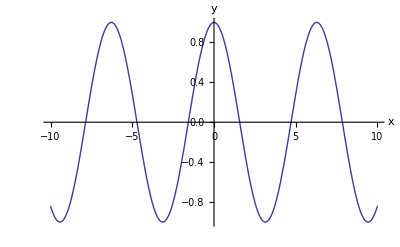

```mathematica
Plot[Cos[x], {x, -10,10},AxesLabel->{x,y}]
```

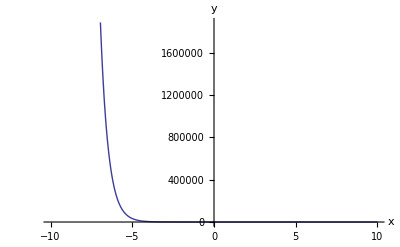

```mathematica
Plot[8^(-x), {x, -10,10},AxesLabel->{x,y}]
```

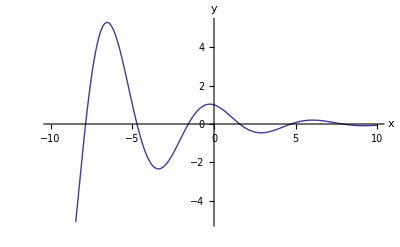

```mathematica
Plot[Cos[x] * 8^(-x/8), {x, -10,10},AxesLabel->{x,y}]
```

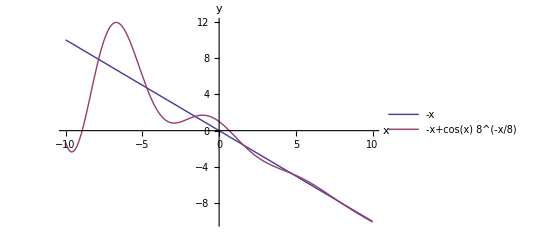

```mathematica
Plot[{-x,-x + Cos[x] * 8^(-x/8) }, {x, -10,10},PlotLegends->"Expressions",AxesLabel->{x,y}]
```

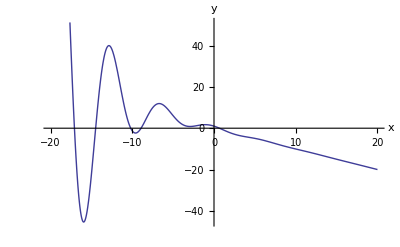

```mathematica
Plot[-x  + Cos[x] * 8^(-x/8), {x, -20,20},AxesLabel->{x,y}]
```

Расчет производных и их графики

```mathematica
df = D[f,x];
df
```

-1-3 2^(-3+(3 (1-x))/8) Cos[3 x] Log[2]-3 2^((3 (1-x))/8) Sin[3 x]

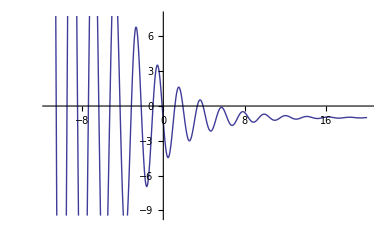

```mathematica
Plot[df, {x,-11.2,19.99}]
```

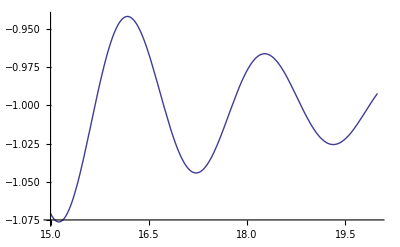

```mathematica
Plot[df, {x,15,19.99}]
```

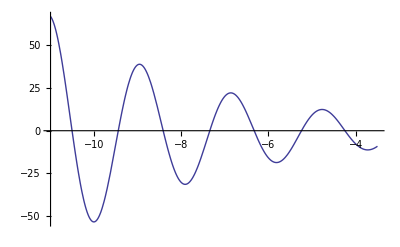

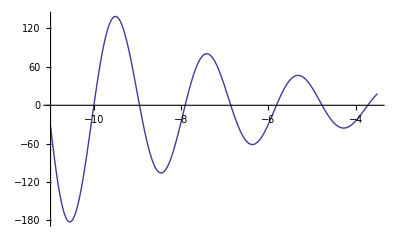

```mathematica
d2f = D[df,x];
Plot[df, {x,-11,-3.5}]
Plot[d2f, {x,-11,-3.5}]
```

```mathematica
d2f
```

-9 2^((3 (1-x))/8) Cos[3 x]+9 2^(-6+(3 (1-x))/8) Cos[3 x] Log[2]^2+9 2^(-2+(3 (1-x))/8) Log[2] Sin[3 x]